```mathematica
SetDirectory[NotebookDirectory[]]
```

/home1/thelfer/Desktop/HigherDim/Code/DIM4

```mathematica
a = Import["general_a202.dat"];
B= Import["general_B202.dat"];
c = Import["general_c202.dat"];
phi = Import["general_phi202.dat"];
```

```mathematica
n= 2*(Length[c [[1,;;]]]-2)
length = Length[c [[;;,1]]]
DeltaL = c [[2,1]]
Subscript[κ, 0]=8 π;
M=1;
Ω  =Sqrt[c[[length,2]]]/a[[length,2]];
ω=Ω/M;
Subscript[r, min]= phi[[1,1]];
Subscript[r, max]= phi[[length,1]];
```

4

12001

0.01

## Extension

```mathematica
ω=1;
Subscript[m, ϕ]=1;
Subscript[r, max2]=Subscript[r, max];
```

```mathematica
Equ1 = D[A1[t,r],t]==Subscript[κ, 0] r A1[t,r]D[ϕ[t,r],t]D[ϕ[t,r],r];
Equ2 =  D[A1[t,r],r]==(Subscript[κ, 0] A1[t,r]r)/2(C[t,r] (D[ϕ[t,r],t])^2+D[ϕ[t,r],r]^2+A1[t,r]Subscript[m, ϕ]^2ϕ[t,r]^2)+A1[t,r]/r(1-A1[t,r]);
Equ3=D[C[t,r],r] == (2 C[t,r])/r(1+A1[t,r](1/2 Subscript[κ, 0] r^2 Subscript[m, ϕ]^2ϕ[t,r]^2-1));
Equ4 = C[t,r]^2 D[ϕ[t,r],{t,2}]==-1/2 D[C[t,r],t]  D[ϕ[t,r],t]*C[t,r]+ D[ϕ[t,r],{r,2}]*C[t,r]+ D[ϕ[t,r],r](2/r*C[t,r]-D[C[t,r],r]/2)-A1[t,r]Subscript[m, ϕ]^2ϕ[t,r]*C[t,r];
```

```mathematica
Subscript[j, max]=2;
```

```mathematica
Sub1[t,r] =(√Subscript[κ, 0])^-1 Sum[Subscript[ϕ, j][r]Cos[j ω t],{j,1,Subscript[j, max],2}];
Sub2[t,r] = Sum[Subscript[A1, j][r]Cos[j ω t],{j,0,Subscript[j, max],2}];
Sub3[t,r] = Sum[Subscript[CS1, j][r]Cos[j ω t],{j,0,Subscript[j, max],2}];
```

```mathematica
Subtemp = {ϕ[t,r]-> Sub1[t,r],A1[t,r]-> Sub2[t,r],C[t,r]-> Sub3[t,r]};
Subtot = Flatten[{Subtemp,D[Subtemp,r],D[Subtemp,t],D[Subtemp,{t,2}],D[Subtemp,{r,2}]}];
Consttemp=First[Solve[TrigReduce[Equ1/.Subtot]/.Sin[2ω t]-> 1/.Sin[__]->0,Subscript[A1, 2][r]]];
Constrain = Flatten[{Consttemp,D[Consttemp,r],D[Consttemp,{r,2}]}];
```

```mathematica
SolveEqu3=Solve[TrigReduce[Equ3/.Subtot]/.Cos[__]->0,Subscript[CS1, 0]'[r]][[1]];
SolveEqu2=Solve[TrigReduce[Equ2/.Subtot]/.Cos[__]->0,Subscript[A1, 0]'[r]][[1]];
Sol4 =First[ Solve[TrigReduce[Equ4/.Subtot]/.Cos[ω t]-> 1/.Cos[__]-> 0/.Constrain,Subscript[ϕ, 1]''[r]]];
Sol30=First[Solve[TrigReduce[Equ3/.Subtot]/.Cos[__]->0/.Constrain,Subscript[CS1, 0]'[r]]];
Sol32=First[Solve[TrigReduce[Equ3/.Subtot]/.Cos[2ω t]->1/.Cos[__]->0/.SolveEqu3/.Constrain,Subscript[CS1, 2]'[r]]];
Sol20=First[Solve[TrigReduce[Equ2/.Subtot]/.Cos[__]->0/.Constrain,Subscript[A1, 0]'[r]]];
```

```mathematica
RHS={Subscript[A1, 0]'[r],Subscript[CS1, 0]'[r],Subscript[A1, 0][Subscript[r, max]],Subscript[CS1, 0][Subscript[r, max]]};
```

```mathematica
LHS={Subscript[A1, 0]'[r]/.Sol20/.Subscript[ϕ, 1]'[r]->ψ[r],Subscript[CS1, 0]'[r]/.Sol30/.Subscript[ϕ, 1]'[r]->ψ[r],a[[length,2]],c[[length,2]]}/.Subscript[CS1, 2][r]->0/.Subscript[ϕ, 1][r]-> 0/.ψ[r]->0;
```

```mathematica
Equa =RHS==LHS
```

{A1_0'[r],CS1_0'[r],A1_0[120.],CS1_0[120.]}=={(128 A1_0[r]-128 A1_0[r]^2)/(128 r),(32 CS1_0[r]-32 A1_0[r] CS1_0[r])/(16 r),1.00052,0.994235}

```mathematica
extension = NDSolve[{Equa},{Subscript[A1, 0][r],Subscript[CS1, 0][r]},{r,Subscript[r, max],Subscript[r, max2]}];
Plot[Subscript[A1, 0][r]/.extension,{r,Subscript[r, max],Subscript[r, max2]}]
Plot[Subscript[ϕ, 1][r]/.extension,{r,Subscript[r, max],Subscript[r, max2]}]
```

Plot::plld: Endpoints for r in {r,120.,120.} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[A1_0[r]/.extension,{r,r_max,r_max2}]

Plot::plld: Endpoints for r in {r,120.,120.} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[ϕ_1[r]/.extension,{r,r_max,r_max2}]

## Data

```mathematica
Ω  =Sqrt[c[[length,2]]]/a[[length,2]];
ω=Ω/M
```

0.996598

```mathematica
Phi= ConstantArray[0,length];
A = ConstantArray[0,length];
CS = ConstantArray[0,length];
grr = ConstantArray[0,length];
alpha = ConstantArray[0,length];
krr = ConstantArray[0,length];
PiM = ConstantArray[0,length];
For[i=1,i<=length,i++,
Phi[[i]]=(√Subscript[κ, 0])^-1 Sum[phi[[i,(j+1)/2+1]]Cos[j ω t],{j,1,n,2}];
A[[i]] = Sum[a[[i,j/2+2]]*Cos[j ω t],{j,0,n,2}];
CS[[i]] = Sum[c[[i,j/2+2]]*Cos[j ω t],{j,0,n,2}];
grr[[i]] = A[[i]];
alpha[[i]]=Ω*Sqrt[A[[i]]/CS[[i]]];
krr[[i]] =  Sum[a[[i,j/2+2]]*D[Cos[j ω t],t],{j,0,n,2}]/(2*alpha[[i]]);
PiM[[i]] = 1/alpha[[i]]*(√Subscript[κ, 0])^-1 Sum[phi[[i,(j+1)/2+1]]*D[Cos[j ω t],t],{j,1,n,2}];
]
```

#### Regularization of solution

```mathematica
Subscript[t, out]=0;0.5*Pi*1/ω
```

1.57616

```mathematica
grr2 = Table[Subscript[A1, 0][r]/.extension[[1]],{r,Subscript[r, max],Subscript[r, max2],DeltaL}];
grr3 = Flatten[{grr/.t-> Subscript[t, out],grr2}];
alpha2  = Table[Ω*Sqrt[Subscript[A1, 0][r]/Subscript[CS1, 0][r]]/.extension ,{r,Subscript[r, max],Subscript[r, max2],DeltaL}];
alpha3 = Flatten[{alpha/.t-> Subscript[t, out],alpha2}];
Zeros =  Table[0.00,{r,Subscript[r, max],Subscript[r, max2],DeltaL}];
PiM3 = Flatten[{PiM/.t-> Subscript[t, out],Zeros}];
krr3 = Flatten[{krr/.t-> Subscript[t, out],Zeros}];
Phi3 = Flatten[{Phi/.t-> Subscript[t, out],Zeros}];
```

```mathematica
Length[Phi3]
```

12002

## Export and testing

```mathematica
Export["alpha001.csv",alpha3]
Export["grr001.csv",grr3]
Export["Phi001.csv",Phi3]
Export["Pi001.csv",PiM3]
Export["Krr001.csv",krr3]
```

alpha001.csv

grr001.csv

Phi001.csv

Pi001.csv

Krr001.csv

```mathematica
Phi=(√Subscript[κ, 0])^-1 Sum[Interpolation[phi[[;;,{1,(j+1)/2+1}]],r]*Cos[j ω t],{j,1,n,2}];
A = Sum[Interpolation[a[[;;,{1,j/2+2}]],r]*Cos[j ω t],{j,0,n,2}];
CS= Sum[Interpolation[c[[;;,{1,j/2+2}]],r]*Cos[j ω t],{j,0,n,2}];
grr= A;
alpha=Ω*Sqrt[A/CS];
```

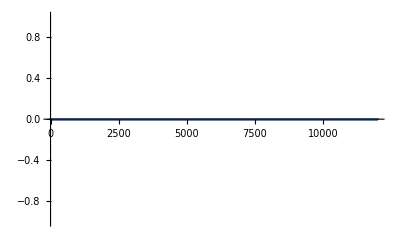

```mathematica
ListPlot[PiM3,PlotRange->All]
```

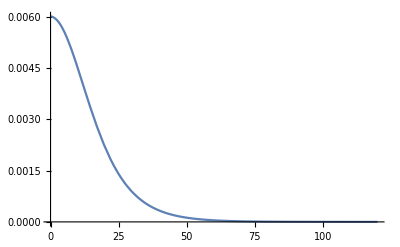

```mathematica
Plot[Phi/.t-> 0,{r,Subscript[r, min],Subscript[r, max]}]
```

```mathematica
r1= 100;
r2 = 120;
A11 = grr/.t-> 0/.r->r1;
A12 = grr/.t-> 0/.r->r2;
vals = {Subscript[r, 1]->r1,Subscript[r, 2]-> r2, Subscript[A1, 1]->A11,Subscript[A1, 2]->A12};
data  =Solve[{Subscript[A1, 1]==(C1-2M1/Subscript[r, 1]^2)^-1,Subscript[A1, 2]==(C1-2M1/Subscript[r, 2]^2)^-1},{M1,C1}][[1]];
M1 /.data/.vals
C1 /.data/.vals
```

3.70986

0.999999

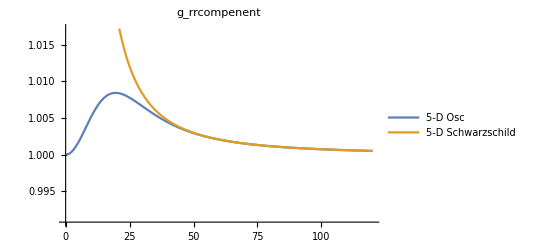

```mathematica
Plot[{grr/.t-> 0,Evaluate[(C1-2M1/r^2)^-1/.data/.vals]},{r,Subscript[r, min],Subscript[r, max]},PlotLegends->{"5-D Osc","5-D Schwarzschild"},PlotLabel->"g_rrcompenent"]
```

```mathematica
N1 = Length[Phi3];
dPhi3dx =( Phi3[[2;;]]- Phi3[[;;(N1-1)]])/DeltaL;
dxgrr3dx = (grr3[[2;;]]- grr3[[;;(N1-1)]])/DeltaL;
rr = phi[[;;,1]];
```

```mathematica
SubX1={α[t,r]->alpha,β[t,r]->grr,D[β[t,r],r]->D[grr,r],ϕ[t,r]->Phi,D[ϕ[t,r],r]^2->D[Phi,r]^2,D[ϕ[t,r],t]^2->D[Phi,t]^2};
```

```mathematica
SubX=Flatten[{SubX1,D[SubX1,r],D[SubX1,{r,2}],D[SubX1,{t,2}],D[SubX1,t]},1];
```

```mathematica
coord={t,r,θ1,θ2,ϕ};
metric=DiagonalMatrix[{-α[t,r]^2,β[t,r],r^2,r^2 Sin[θ1]^2,r^2 Sin[θ1]^2Sin[θ2]^2}];
$Assumptions=And[t∈Reals,r∈Reals,r>0,θ>0,θ<π,ϕ∈Reals];
metricsign=-1;
<<diffgeo.m;
```

```mathematica
▽ϕ=covariant[ϕ[t,r]];
V[x_]=1/2 M^2x^2;
L=-ComplexExpand[1/2(▽ϕ).raise[▽ϕ]+V[ϕ[t,r]]];
Eom=Simplify[-((-scalarLaplacian[ϕ[t,r]]+(D[V[x],x]/.x->ϕ[t,r])))];
T=((▽ϕ)**▽ϕ)+metric (L);
T//MatrixForm
```

((ϕ^(1,0)[t,r])^2-α[t,r]^2 (-1/2 ϕ[t,r]^2-((ϕ^(0,1)[t,r])^2)/(2 β[t,r])+((ϕ^(1,0)[t,r])^2)/(2 α[t,r]^2)) | ϕ^(0,1)[t,r] ϕ^(1,0)[t,r] | 0 | 0 | 0
ϕ^(0,1)[t,r] ϕ^(1,0)[t,r] | (ϕ^(0,1)[t,r])^2+β[t,r] (-1/2 ϕ[t,r]^2-((ϕ^(0,1)[t,r])^2)/(2 β[t,r])+((ϕ^(1,0)[t,r])^2)/(2 α[t,r]^2)) | 0 | 0 | 0
0 | 0 | r^2 (-1/2 ϕ[t,r]^2-((ϕ^(0,1)[t,r])^2)/(2 β[t,r])+((ϕ^(1,0)[t,r])^2)/(2 α[t,r]^2)) | 0 | 0
0 | 0 | 0 | r^2 Sin[θ1]^2 (-1/2 ϕ[t,r]^2-((ϕ^(0,1)[t,r])^2)/(2 β[t,r])+((ϕ^(1,0)[t,r])^2)/(2 α[t,r]^2)) | 0
0 | 0 | 0 | 0 | r^2 Sin[θ1]^2 Sin[θ2]^2 (-1/2 ϕ[t,r]^2-((ϕ^(0,1)[t,r])^2)/(2 β[t,r])+((ϕ^(1,0)[t,r])^2)/(2 α[t,r]^2)))

```mathematica
Res = Abs[8π T -Einstein] ;
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

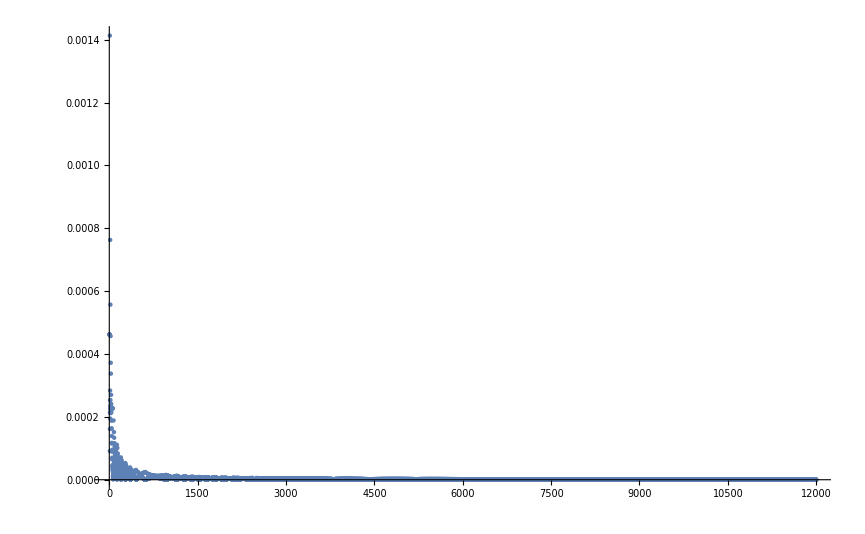

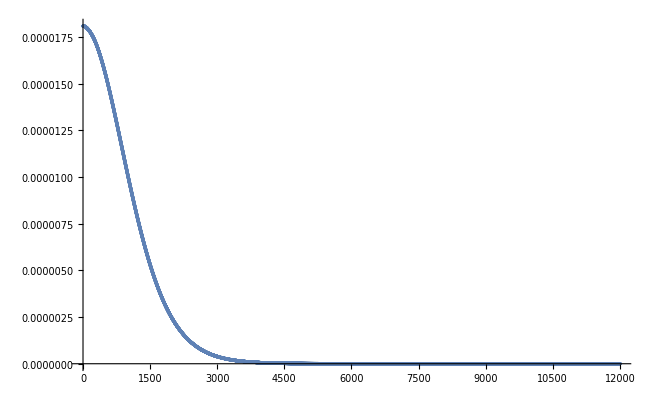

```mathematica
Res11= Res [[1,1]]/.{ ϕ[t,r]->Phi3[[;;(N1-1)]],Derivative[0,1][ϕ][t,r]->dPhi3dx,(Derivative[1,0][ϕ][t,r])^2-> 0, α[t,r]-> alpha3[[;;(N1-1)]],β[t,r]-> grr3[[;;(N1-1)]], Derivative[0,1][β][t,r]-> dxgrr3dx,r->rr};
rho = T[[1,1]]/.{ ϕ[t,r]->Phi3[[;;(N1-1)]],Derivative[0,1][ϕ][t,r]->dPhi3dx,(Derivative[1,0][ϕ][t,r])^2-> 0, α[t,r]-> alpha3[[;;(N1-1)]],β[t,r]-> grr3[[;;(N1-1)]], Derivative[0,1][β][t,r]-> dxgrr3dx,r->rr};
ListPlot[Res11,PlotRange->All]
ListPlot[rho,PlotRange->All]
```

```mathematica
(*HamList = Table[{r,Res11},{r,Subscript[r, min]+4*DeltaL,20,DeltaL}];
RelHam = Table[{r,Res11/rho},{r,Subscript[r, min]+4*DeltaL,20,DeltaL}];*)
```

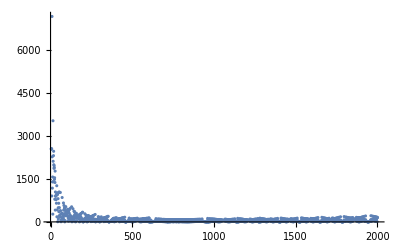

```mathematica
ListPlot[RelHam*100,PlotRange->All]
```

```mathematica
rhototal
```

rhototal

```mathematica
rhototal = NIntegrate[2*Pi^2*r^3*T[[t,t]]/.SubX/.t->0,{r,Subscript[r, min],Subscript[r, max]}]
```

8.70394

```mathematica
(*Potential Energy*)
```

```mathematica
NIntegrate[2*Pi^2*r^3*0.5*(Phi/.t->0)^2,{r,Subscript[r, min],Subscript[r, max]}]
```

8.70335

```mathematica
(*Gravitational Poential Energy*)
```

```mathematica
NIntegrate[2*Pi^2*r*0.5*(Phi/.t->0)^2,{r,Subscript[r, min],Subscript[r, max]}]
```

0.03541